Približna vrednost za π:3.14424

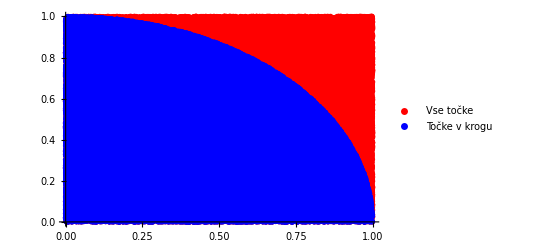

```mathematica
(*Main.nb*)
Get["C:\\Users\\tomaz\\OneDrive\\Dokumenti\\Fakulteta za strojništvo\\3.letnik 1 semester\\Napredna računalniška orodja\\Naloga 2\\MonteCarloPi.m"]

n=100000;(*Število naključnih točk*)

approxPi=MonteCarloPi[n];
Print["Približna vrednost za π:",approxPi]

(*Grafični prikaz*)

points=Table[{RandomReal[],RandomReal[]},{i,n}];
insidePoints=Select[points,#[[1]]^2+#[[2]]^2<=1&];

ListPlot[{points,insidePoints},PlotStyle->{{PointSize[0.01],Red},{PointSize[0.01],Blue}},AxesOrigin->{0,0},PlotLegends->{"Vse točke","Točke v krogu"}]
```